```mathematica
Clear["p","m","x","g","gg","λ","Δt","length","rnd","θ"]
$Assumptions=x>0&&x∈Reals&&λ>0&&λ∈Reals;
SeedRandom[1]
```

```mathematica
𝒟=HalfNormalDistribution[θ=√π];
p=PDF[𝒟,x]
m=Mean[𝒟]
K2=FullSimplify[-2 λ/p Integrate[(x-m)p,{x,0,x}]](*g^2[x]*)
g[x_]=Sqrt[K2]
gg[x_]=FullSimplify[Sqrt[K2] D[Sqrt[K2],x]]
```

Piecewise[{{(2 ⅇ^(-x^2))/(√π), x>0}, {0, True}}]

1/(√π)

λ-ⅇ^(x^2) λ Erfc[x]

√(λ-ⅇ^(x^2) λ Erfc[x])

λ (1/(√π)-ⅇ^(x^2) x Erfc[x])

```mathematica
θ=√π;
λ=50;
Δt=1/10000;
length = 5 10^6;
rnd=RandomVariate[NormalDistribution[],length];
ξ[n_Integer]:=rnd[[n]]
vals=Flatten[RecurrenceTable[{y[n+1]==1/(1+λ Δt)(y[n]+ λ m Δt+g[y[n]] √Δt ξ[n]+1/2 gg[y[n]]Δt(ξ[n]^2-1)),y[1]==1},{y},{n,1,length}]];
```

-Graphics-

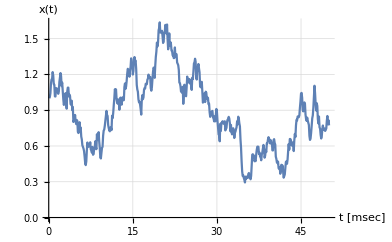

{0.560259,0.422411,0.00105407,3.32923}

```mathematica
normFactor = CovarianceFunction[vals,0];
autocorrelationPlot=ListLinePlot[
{ParallelTable[{z Δt 10^3,CovarianceFunction[vals,z]/normFactor},{z,0,500,25}],
Table[{z Δt 10^3,Exp[-z Δt λ ]},{z,0,500,25}]},PlotRange->Full,GridLines->Automatic,
PlotLegends->Placed[{"Simulation","Exp[-λτ]"},{.8,.8}],AxesLabel->{"τ [msec]","C_xx(τ)"},LabelStyle -> Directive[Black,13,FontFamily->"Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],PlotMarkers->{{Graphics[{Disk[]}],.04},""}]
timePlot=ListLinePlot[Thread[{Table[Δt x,{x,1,500}] 10^3,vals[[1;;500]]}],LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],
AxesLabel->{"t [msec]","x(t)"},GridLines->Automatic
]
{Mean[vals],StandardDeviation[vals],Min[vals],Max[vals]}
```

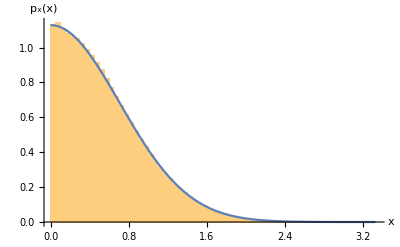

```mathematica
h1= Histogram[vals,50,"ProbabilityDensity",ChartLegends->Placed[SwatchLegend[{"Hist"}],Scaled[{.5,.9}]],PerformanceGoal->"Speed"];
h3= Histogram[vals,75,"ProbabilityDensity",PlotRange->{{2.3,Max[vals]},{0,5 10^-3}},PlotRangePadding->Automatic,PerformanceGoal->"Speed",AxesOrigin->{Max[vals]-.2,0},Ticks->{Automatic,Table[{i,ScientificForm[N@i,3]},{i,0,5 10^-3,5 10^-3/2}]}];
h2=Plot[PDF[𝒟,x],{x,0,Max[vals]},PlotLegends->Placed[LineLegend[{"PDF"}],Scaled[{.5,.9}]]];
h4=Plot[PDF[𝒟,x],{x,2.3,Max[vals]}];
pdfPlot=Show[h1,h2,LabelStyle -> Directive[Black,13,FontFamily-> "Times New Roman"],AxesLabel-> {"x","p_x(x)"},
TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"],Epilog-> Inset[Show[h3,h4,TicksStyle->Directive[Black, 13,FontFamily-> "Times New Roman"]],Scaled[{.8,.5}],Automatic,Automatic]]
```

200

The null hypothesis that the data is distributed according to the HalfNormalDistribution[√π] is not rejected at the 0.1 percent level based on the Cramér-von Mises test.

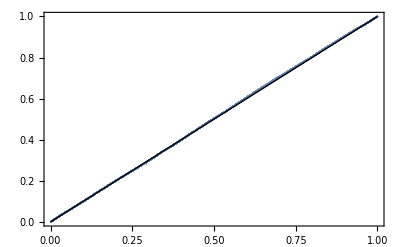

```mathematica
step = Round[1/(λ Δt)]
DistributionFitTest[vals[[1;;;;step]],𝒟,"TestConclusion",SignificanceLevel->0.001]
ProbabilityPlot[vals[[1;;;;step]],𝒟]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["autocorrelationPlotHN.pdf",autocorrelationPlot]; Export["autocorrelationPlotHN.png",autocorrelationPlot];
Export["timePlotHN.pdf",timePlot]; Export["timePlotHN.png",timePlot];
Export["pdfPlotHN.pdf",pdfPlot];Export["pdfPlotHN.png",pdfPlot];
```